```mathematica
(*Лабораторная работа №6, Дзебан Арсений 0В21*)
```

```mathematica
DSolve[D[u[x,y],x]==D[u[x,y],y], u, {x,y}]
```

{{u→Function[{x,y},C[1][x+y]]}}

```mathematica
(*Базовое решение уравнения*)sol=DSolve[D[u[x,y],x]==D[u[x,y],y],u,{x,y}];

(*Замена C[1] на разные функции*)
solutions={(u[x,y]/. sol[[1]])/. {C[1][e_]:>Sin[e]},(u[x,y]/. sol[[1]])/. {C[1][e_]:>Cos[e]},(u[x,y]/. sol[[1]])/. {C[1][e_]:>Exp[e]},(u[x,y]/. sol[[1]])/. {C[1][e_]:>Log[e+1]},(u[x,y]/. sol[[1]])/. {C[1][e_]:>e^2},(u[x,y]/. sol[[1]])/. {C[1][e_]:>e^3-e}}
```

{Sin[x+y],Cos[x+y],ⅇ^(x+y),Log[1+x+y],(x+y)^2,-x-y+(x+y)^3}

```mathematica
Plot3D[solutions[[1]], {x,-5,5}, {y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[solutions[[2]], {x,-5,5}, {y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[solutions[[3]], {x,-5,5}, {y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[solutions[[4]], {x,-5,5}, {y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[solutions[[5]], {x,-5,5}, {y,-5,5}]
```

-Graphics3D-

```mathematica
sol2 = DSolve[x*D[u[x,y],x]+ (y+x^2)*D[u[x,y],y] == u[x,y], u, {x,y}]
```

{{u→Function[{x,y},x C[1][-x+y/x]]}}

```mathematica
sol2[[1,1,2,2]]
```

x C[1][-x+y/x]

```mathematica
generalSolution=u[x,y]/. sol2[[1]];

(*Замена C[1] на разные функции*)
solutions2={generalSolution/. {C[1][e_]:>Sin[e]},generalSolution/. {C[1][e_]:>Cos[e]},generalSolution/. {C[1][e_]:>Exp[e]}};

(*Вывод решений*)
solutions2
```

{-x Sin[x-y/x],x Cos[x-y/x],ⅇ^(-x+y/x) x}

```mathematica
Plot3D[solutions2⟦1⟧,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[solutions2⟦2⟧,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[solutions2⟦3⟧,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
koshi = DSolveValue[x*D[u[x,y],x]+ (y+x^2)*D[u[x,y],y] == u[x,y] && u[x,x] == x^2, u, {x,y}]
```

Function[{x,y},x+x^2-y]

```mathematica
f2 = Plot3D[koshi[[2]], {x,-5,5},{y,-5,5}]
```

-Graphics3D-

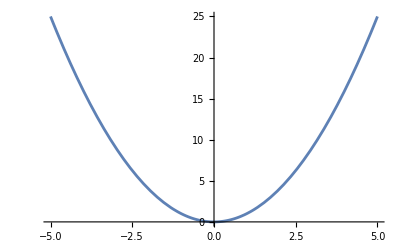

```mathematica
Plot[x^2, {x,-5,5}]
```

```mathematica
f1 = ParametricPlot3D[{s,s,s^2},{s,-5,5}];
Show[f1,f2]
```

-Graphics3D-